## Example I Coherent States of the Harmonic Oscillator

```mathematica
<<QuantumAlgebra`QuantumAlgebra`
```

### The Harmonic Oscillator

The Hamiltonian of a single particle of mass m placed in an harmonic potential is obtained by replacing the classical position and momentum variables with the corresponding position and momentum operators 𝒫̂ and 𝒳̂.

```mathematica
ℋ̂=1/(2m)(𝒫̂)^2+(m ω^2)/2(𝒳̂)^2;
```

where ω is the natural frecuency of the particle. The momentm and position operators satisfy the following commutation relation:

```mathematica
QASet[[𝒳̂,𝒫̂]_-=ⅈ ℏ OverHat[1]]
```

The problem of finding the eigenvalues for this Hamiltonian is nicely solved by introducing creation and annihilation operators, which are related to the position and mometum operators according to the folowing rule:

```mathematica
rule1={SuperDagger[â]->(√((m ω)/(2ℏ))X̂-ⅈ/(√(2m ℏ ω))P̂),â->(√((m ω)/(2ℏ))X̂+ⅈ/(√(2m ℏ ω))P̂)};
```

the inverse relation is

```mathematica
rule2=Solve[{SuperDagger[â]==(√((m ω)/(2ℏ))X̂-ⅈ/(√(2m ℏ ω))P̂),â==(√((m ω)/(2ℏ))X̂+ⅈ/(√(2m ℏ ω))P̂)},{X̂,P̂}][[1]]//Simplify
```

{X̂→(â+(â)^†)/(√2 √((m ω)/ℏ)),P̂→-(ⅈ √(m ω ℏ) (â-(â)^†))/(√2)}

From the commutation relation for momentum and position operators the commuttion relation for these new operators can be found

```mathematica
[â,SuperDagger[â]]_-/.rule1//PowerExpand
```

OverHat[1]

We implement this commutator as a definition

```mathematica
QASet[ [â,SuperDagger[â]]_-=OverHat[1] ]
```

The replacing hamiltonian reduces to

```mathematica
Ĥ/.rule2//QAPowerExpand//Factor//QAOrdering[#,{SuperDagger[â],â}]&
```

1/2 ω ℏ (2 (â)^†·â+OverHat[1])

So the problem of finding eigenstates of the HO reduces to find the eigenstates of the number operator defined as

```mathematica
𝒩̂=SuperDagger[â]·â ;
```

This problem can be solved and what one obtains is a set of infinite eigenstates labeled as   |n⟩ with eigenvalue n, where the allowed values fo n are n=0,1,2…This solutions for a basis in the hilbert space

```mathematica
KD[n_,n_]:=1
KD[n_+k_,n_]:=0
KD[n_,n_+k_]:=0
KD[n_?NumberQ,m_?NumberQ]:=0
```

```mathematica
⟨n_|m_⟩:=KD[n,m]
```

The action of 𝒶̂,(â)^† on these eigenstates can be found, and we introduce them as defintions to work with

```mathematica
QASet[Operator/: â**|n_⟩:=√n|n-1⟩]
```

```mathematica
QASet[Operator/: SuperDagger[â]**|n_⟩:=√(n+1)|n+1⟩]
```

```mathematica
Ket/:SuperDagger[Subscript[â, k_]]·(|n_⟩)_k_:=√(n+1)(|n⟩)_k
Ket/:Subscript[â, k_]·(|n_⟩)_k_:=√n(|n⟩)_k/;n≥0
```

Now let's try to combine the definition we made for the Fock states and the ones for the creation and annihilation operators to compute the expectation value of (â+(â)^†) and (â+(â)^†)^2. We assume that the state of the system is a Fock state with n excitations.

```mathematica
⟨n|·(â+SuperDagger[â])·|n⟩
```

√n ⟨n|-1+n⟩+⟨-1+n|n⟩ (√n)^*

```mathematica
⟨n|·(â+SuperDagger[â])^2·|n⟩//QAPowerExpand
```

1+2 n

By the way, note that although bras appear in the computation we didn't did any definition for them. They are not infered from our definitions.

```mathematica
⟨n|·â
```

⟨n|·â

The operators are acting to the right. Of course, if needed we can setup definitions for operators acting on bras, in the same manner we did for kets. Also, we will see later that it's possible to set up some definitions and let QuantumAlgebra to infer some consecuences.

### Definition of coherent states

Coherent states are well known as quasi-classical states for the harmonic oscillator. This state  can be expressed as a linear superposition of the infinite fock states which are eigenstates of the harmonic oscillator hamiltonian.

Formally a coherent state is an eigenstate of the annihilation operator. We can introduce it as a definition to work with.

```mathematica
QASet[ â·(|a_⟩)_α=a(|a⟩)_α ]
```

Note that the eigenkets of the annihilation operator have a subscript label "α", so they are not confused with the engeinkets of the number operator.

Expanding the coherent state in the fock basis and applying the annihilation operator we have (sum over n is implied on the r.h.s of equation)

```mathematica
â·(|α⟩)_α==â·(c[n]|n⟩)
```

α (|α⟩)_α==√n c[n] |-1+n⟩

where the sum on the hand r.h.s of equation runs from 1to ∞. Replacing the expansion for the coherent state on the l.h.s shifted by one so it too runs from 1 to ∞ we have

```mathematica
α (|α⟩)_α==√n c[n] |-1+n⟩/.(|α⟩)_α->c[n-1]|n-1⟩
```

α c[-1+n] |-1+n⟩==√n c[n] |-1+n⟩

the solution of the last equation gives the following expression (sum over n implied)

```mathematica
(|α⟩)_α=α^n/(√(n!))Subscript[c, 0]|n⟩;
```

and the correspondent bra

```mathematica
_α⟨α|=(SuperStar[α])^m/(√(m!))SuperStar[c0]⟨m|;
```

normalization of the coherent state assuming that c0 is real gives a simple equation to solve (sum over n on the r.h.s)

```mathematica
_α⟨α|·(|α⟩)_α==1
```

(α^n c0^* (α^*)^m KroneckerDelta[m,n] c_0)/(√(m!) √(n!))==1

This sum is, of course the exponential

```mathematica
∑_(n=0)^∞ (c0 α^n SuperStar[c0] (SuperStar[α])^n)/(n!)==1
```

c0 ⅇ^(α α^*) c0^*==1

So we got our final expression for a coherent state

(|α⟩)_α=ⅇ^(-| α |^2/ 2)∑_(n=0)^∞ α^n/(√(n!))|n⟩

### Coherent states: minimun uncertainty states

Before going on, we clear the definition of the coherent state in terms of fock states. We also enter the normalization of coherent states to work automatically

```mathematica
(|α⟩)_α=. ;          _α⟨α|=.;             _α Subscript[⟨a_|a_⟩, α]=1;
```

The expectation values of the position operator and its square when the system is in a coherent state can be calulated as

```mathematica
Subscript[⟨X⟩, α]=_α⟨α|·X̂·(|α⟩)_α/.rule2//PowerExpand//FullSimplify
```

(√2 √ℏ Re[α])/(√m √ω)

```mathematica
Subscript[⟨X^2⟩, α]=_α⟨α|·(X̂)^2·(|α⟩)_α/.rule2//QAPowerExpand//
					QAOrdering[#,{SuperDagger[â],â}]&//FullSimplify
```

1/(2 m ω)ℏ (1+α^2+2 α α^*+(α^*)^2)

the uncertainty in the position is given by

```mathematica
Δx=√(Subscript[⟨X^2⟩, α]-Subscript[⟨X⟩, α]^2)//FullSimplify//PowerExpand
```

(√ℏ)/(√2 √m √ω)

Similarly the expectation values of the momentum operator and its square when the system is in a coherent state can be calulated as

```mathematica
Subscript[⟨P⟩, α]=_α⟨α|·P̂·(|α⟩)_α/.rule2//Factor//
					PowerExpand//FullSimplify
```

√2 √m √ω √ℏ Im[α]

```mathematica
Subscript[⟨P^2⟩, α]=_α⟨α|·(P̂)^2·(|α⟩)_α/.rule2//QAPowerExpand//
					QAOrdering[#,{SuperDagger[â],â}]&//FullSimplify
```

-1/2 m ω ℏ (-1+α^2-2 α α^*+(α^*)^2)

and the uncertainty in the momentum give us

```mathematica
Δp=√(Subscript[⟨P^2⟩, α]-Subscript[⟨P⟩, α]^2)//FullSimplify//PowerExpand
```

(√m √ω √ℏ)/(√2)

with those results the product of the uncertainties gives the minimun value

```mathematica
Δx Δp
```

ℏ/2

### The displacement operator

We define the displacement operators as

```mathematica
𝒟[α_]:=Exp[α SuperDagger[â]-SuperStar[α] â]
```

let's apply this operator to the vacuum fock state

```mathematica
𝒟[α]·|0⟩//BCHRelation
```

ⅇ^(-(α α^*)/2) ⅇ^(α (â)^†)·ⅇ^(-α^* â)·|0⟩

expanding in series both exponential (note that we need to expand the powers because we have not defined rules for the action of powers of â,(â)^†on fock states, thus we have to apply one operator each time to the vacuum)

```mathematica
exp1=QASeries[ⅇ^(-SuperStar[α] â),{â,0,6}]//QAPowerExpand;
```

```mathematica
exp2=QASeries[ⅇ^(α SuperDagger[â]),{SuperDagger[â],0,6}]//QAPowerExpand;
```

thus we have

```mathematica
ⅇ^(-(α SuperStar[α])/2) exp2·exp1·|0⟩//ReleaseHold
```

ⅇ^(-(α α^*)/2) (|0⟩+α |1⟩+(α^2 |2⟩)/(√2)+(α^3 |3⟩)/(√6)+(α^4 |4⟩)/(2 √6)+(α^5 |5⟩)/(2 √30)+(α^6 |6⟩)/(12 √5))

this is not other thing, but the definition of the coherent state in terms of fock states. So we state that the displacement operator applied on vacuum generates a coherent state

(|α⟩)_α=𝒟(α)| 0⟩=ⅇ^(-| α |^2/ 2)∑_(n=0)^∞ α^n/(√(n!))|n⟩

One over property of the displacement operator can be derived using the expansion formula for expressions like ⅇ^(Â)B̂ ⅇ^(-Â) as explained in part 7

```mathematica
QASeries[ SuperDagger[𝒟[α]]·â·𝒟[α],10]//ReleaseHold
```

α OverHat[1]+â

```mathematica
QASeries[ SuperDagger[𝒟[α]]·SuperDagger[â]·𝒟[α],10]//ReleaseHold
```

α^* OverHat[1]+(â)^†

```mathematica
|α_,i_,nmax_⟩:=∑_(n=0)^nmax (Exp[-Abs[α]^2/2] α^n)/(√(n!))|Subscript[n, i]⟩
⟨α_,i_,nmax_|:=∑_(n=0)^nmax (Exp[-Abs[α]^2/2](SuperStar[α])^n)/(√(n!))⟨Subscript[n, i]|
```

```mathematica
|2.0,1,15⟩
```

0.135335 |0_1⟩+0.270671 |1_1⟩+0.382786 |2_1⟩+0.442003 |3_1⟩+0.442003 |4_1⟩+0.39534 |5_1⟩+0.322793 |6_1⟩+0.244009 |7_1⟩+0.17254 |8_1⟩+0.115027 |9_1⟩+0.0727494 |10_1⟩+0.0438695 |11_1⟩+0.0253281 |12_1⟩+0.0140495 |13_1⟩+0.00750977 |14_1⟩+0.00387803 |15_1⟩

```mathematica
|ψ⟩=|2.0,1,15⟩⊗|2.0,1,15⟩
```

0.0183156 |0_1,0_1⟩+0.0732626 |0_1,1_1⟩+0.103609 |0_1,2_1⟩+0.119637 |0_1,3_1⟩+0.119637 |0_1,4_1⟩+0.107007 |0_1,5_1⟩+0.0873707 |0_1,6_1⟩+0.066046 |0_1,7_1⟩+0.0467016 |0_1,8_1⟩+0.0311344 |0_1,9_1⟩+0.0196911 |0_1,10_1⟩+0.0118742 |0_1,11_1⟩+0.00685557 |0_1,12_1⟩+0.00380279 |0_1,13_1⟩+0.00203267 |0_1,14_1⟩+0.00104967 |0_1,15_1⟩+0.0732626 |1_1,1_1⟩+0.207218 |1_1,2_1⟩+0.239275 |1_1,3_1⟩+0.239275 |1_1,4_1⟩+0.214014 |1_1,5_1⟩+0.174741 |1_1,6_1⟩+0.132092 |1_1,7_1⟩+0.0934032 |1_1,8_1⟩+0.0622688 |1_1,9_1⟩+0.0393822 |1_1,10_1⟩+0.0237484 |1_1,11_1⟩+0.0137111 |1_1,12_1⟩+0.00760557 |1_1,13_1⟩+0.00406535 |1_1,14_1⟩+0.00209934 |1_1,15_1⟩+0.146525 |2_1,2_1⟩+0.338385 |2_1,3_1⟩+0.338385 |2_1,4_1⟩+0.302661 |2_1,5_1⟩+0.247122 |2_1,6_1⟩+0.186806 |2_1,7_1⟩+0.132092 |2_1,8_1⟩+0.0880614 |2_1,9_1⟩+0.0556949 |2_1,10_1⟩+0.0335853 |2_1,11_1⟩+0.0193905 |2_1,12_1⟩+0.0107559 |2_1,13_1⟩+0.00574927 |2_1,14_1⟩+0.00296891 |2_1,15_1⟩+0.195367 |3_1,3_1⟩+0.390734 |3_1,4_1⟩+0.349483 |3_1,5_1⟩+0.285351 |3_1,6_1⟩+0.215705 |3_1,7_1⟩+0.152527 |3_1,8_1⟩+0.101685 |3_1,9_1⟩+0.0643109 |3_1,10_1⟩+0.038781 |3_1,11_1⟩+0.0223902 |3_1,12_1⟩+0.0124198 |3_1,13_1⟩+0.00663869 |3_1,14_1⟩+0.0034282 |3_1,15_1⟩+0.195367 |4_1,4_1⟩+0.349483 |4_1,5_1⟩+0.285351 |4_1,6_1⟩+0.215705 |4_1,7_1⟩+0.152527 |4_1,8_1⟩+0.101685 |4_1,9_1⟩+0.0643109 |4_1,10_1⟩+0.038781 |4_1,11_1⟩+0.0223902 |4_1,12_1⟩+0.0124198 |4_1,13_1⟩+0.00663869 |4_1,14_1⟩+0.0034282 |4_1,15_1⟩+0.156293 |5_1,5_1⟩+0.255226 |5_1,6_1⟩+0.192933 |5_1,7_1⟩+0.136424 |5_1,8_1⟩+0.0909494 |5_1,9_1⟩+0.0575215 |5_1,10_1⟩+0.0346867 |5_1,11_1⟩+0.0200264 |5_1,12_1⟩+0.0111086 |5_1,13_1⟩+0.00593782 |5_1,14_1⟩+0.00306628 |5_1,15_1⟩+0.104196 |6_1,6_1⟩+0.157529 |6_1,7_1⟩+0.11139 |6_1,8_1⟩+0.0742599 |6_1,9_1⟩+0.0469661 |6_1,10_1⟩+0.0283216 |6_1,11_1⟩+0.0163515 |6_1,12_1⟩+0.00907017 |6_1,13_1⟩+0.00484821 |6_1,14_1⟩+0.00250361 |6_1,15_1⟩+0.0595404 |7_1,7_1⟩+0.0842028 |7_1,8_1⟩+0.0561352 |7_1,9_1⟩+0.035503 |7_1,10_1⟩+0.0214091 |7_1,11_1⟩+0.0123606 |7_1,12_1⟩+0.00685641 |7_1,13_1⟩+0.0036649 |7_1,14_1⟩+0.00189255 |7_1,15_1⟩+0.0297702 |8_1,8_1⟩+0.0396936 |8_1,9_1⟩+0.0251044 |8_1,10_1⟩+0.0151385 |8_1,11_1⟩+0.00874024 |8_1,12_1⟩+0.00484821 |8_1,13_1⟩+0.00259148 |8_1,14_1⟩+0.00133823 |8_1,15_1⟩+0.0132312 |9_1,9_1⟩+0.0167363 |9_1,10_1⟩+0.0100924 |9_1,11_1⟩+0.00582683 |9_1,12_1⟩+0.00323214 |9_1,13_1⟩+0.00172765 |9_1,14_1⟩+0.000892156 |9_1,15_1⟩+0.00529248 |10_1,10_1⟩+0.00638297 |10_1,11_1⟩+0.00368521 |10_1,12_1⟩+0.00204419 |10_1,13_1⟩+0.00109266 |10_1,14_1⟩+0.000564249 |10_1,15_1⟩+0.00192454 |11_1,11_1⟩+0.00222226 |11_1,12_1⟩+0.00123269 |11_1,13_1⟩+0.000658901 |11_1,14_1⟩+0.000340255 |11_1,15_1⟩+0.000641512 |12_1,12_1⟩+0.000711694 |12_1,13_1⟩+0.000380416 |12_1,14_1⟩+0.000196446 |12_1,15_1⟩+0.000197388 |13_1,13_1⟩+0.000211017 |13_1,14_1⟩+0.000108969 |13_1,15_1⟩+0.0000563967 |14_1,14_1⟩+0.0000582462 |14_1,15_1⟩+0.0000150391 |15_1,15_1⟩

```mathematica
⟨ψ|=(|ψ⟩)^†
```

0.0183156 ⟨0_1,0_1|+0.0732626 ⟨0_1,1_1|+0.103609 ⟨0_1,2_1|+0.119637 ⟨0_1,3_1|+0.119637 ⟨0_1,4_1|+0.107007 ⟨0_1,5_1|+0.0873707 ⟨0_1,6_1|+0.066046 ⟨0_1,7_1|+0.0467016 ⟨0_1,8_1|+0.0311344 ⟨0_1,9_1|+0.0196911 ⟨0_1,10_1|+0.0118742 ⟨0_1,11_1|+0.00685557 ⟨0_1,12_1|+0.00380279 ⟨0_1,13_1|+0.00203267 ⟨0_1,14_1|+0.00104967 ⟨0_1,15_1|+0.0732626 ⟨1_1,1_1|+0.207218 ⟨1_1,2_1|+0.239275 ⟨1_1,3_1|+0.239275 ⟨1_1,4_1|+0.214014 ⟨1_1,5_1|+0.174741 ⟨1_1,6_1|+0.132092 ⟨1_1,7_1|+0.0934032 ⟨1_1,8_1|+0.0622688 ⟨1_1,9_1|+0.0393822 ⟨1_1,10_1|+0.0237484 ⟨1_1,11_1|+0.0137111 ⟨1_1,12_1|+0.00760557 ⟨1_1,13_1|+0.00406535 ⟨1_1,14_1|+0.00209934 ⟨1_1,15_1|+0.146525 ⟨2_1,2_1|+0.338385 ⟨2_1,3_1|+0.338385 ⟨2_1,4_1|+0.302661 ⟨2_1,5_1|+0.247122 ⟨2_1,6_1|+0.186806 ⟨2_1,7_1|+0.132092 ⟨2_1,8_1|+0.0880614 ⟨2_1,9_1|+0.0556949 ⟨2_1,10_1|+0.0335853 ⟨2_1,11_1|+0.0193905 ⟨2_1,12_1|+0.0107559 ⟨2_1,13_1|+0.00574927 ⟨2_1,14_1|+0.00296891 ⟨2_1,15_1|+0.195367 ⟨3_1,3_1|+0.390734 ⟨3_1,4_1|+0.349483 ⟨3_1,5_1|+0.285351 ⟨3_1,6_1|+0.215705 ⟨3_1,7_1|+0.152527 ⟨3_1,8_1|+0.101685 ⟨3_1,9_1|+0.0643109 ⟨3_1,10_1|+0.038781 ⟨3_1,11_1|+0.0223902 ⟨3_1,12_1|+0.0124198 ⟨3_1,13_1|+0.00663869 ⟨3_1,14_1|+0.0034282 ⟨3_1,15_1|+0.195367 ⟨4_1,4_1|+0.349483 ⟨4_1,5_1|+0.285351 ⟨4_1,6_1|+0.215705 ⟨4_1,7_1|+0.152527 ⟨4_1,8_1|+0.101685 ⟨4_1,9_1|+0.0643109 ⟨4_1,10_1|+0.038781 ⟨4_1,11_1|+0.0223902 ⟨4_1,12_1|+0.0124198 ⟨4_1,13_1|+0.00663869 ⟨4_1,14_1|+0.0034282 ⟨4_1,15_1|+0.156293 ⟨5_1,5_1|+0.255226 ⟨5_1,6_1|+0.192933 ⟨5_1,7_1|+0.136424 ⟨5_1,8_1|+0.0909494 ⟨5_1,9_1|+0.0575215 ⟨5_1,10_1|+0.0346867 ⟨5_1,11_1|+0.0200264 ⟨5_1,12_1|+0.0111086 ⟨5_1,13_1|+0.00593782 ⟨5_1,14_1|+0.00306628 ⟨5_1,15_1|+0.104196 ⟨6_1,6_1|+0.157529 ⟨6_1,7_1|+0.11139 ⟨6_1,8_1|+0.0742599 ⟨6_1,9_1|+0.0469661 ⟨6_1,10_1|+0.0283216 ⟨6_1,11_1|+0.0163515 ⟨6_1,12_1|+0.00907017 ⟨6_1,13_1|+0.00484821 ⟨6_1,14_1|+0.00250361 ⟨6_1,15_1|+0.0595404 ⟨7_1,7_1|+0.0842028 ⟨7_1,8_1|+0.0561352 ⟨7_1,9_1|+0.035503 ⟨7_1,10_1|+0.0214091 ⟨7_1,11_1|+0.0123606 ⟨7_1,12_1|+0.00685641 ⟨7_1,13_1|+0.0036649 ⟨7_1,14_1|+0.00189255 ⟨7_1,15_1|+0.0297702 ⟨8_1,8_1|+0.0396936 ⟨8_1,9_1|+0.0251044 ⟨8_1,10_1|+0.0151385 ⟨8_1,11_1|+0.00874024 ⟨8_1,12_1|+0.00484821 ⟨8_1,13_1|+0.00259148 ⟨8_1,14_1|+0.00133823 ⟨8_1,15_1|+0.0132312 ⟨9_1,9_1|+0.0167363 ⟨9_1,10_1|+0.0100924 ⟨9_1,11_1|+0.00582683 ⟨9_1,12_1|+0.00323214 ⟨9_1,13_1|+0.00172765 ⟨9_1,14_1|+0.000892156 ⟨9_1,15_1|+0.00529248 ⟨10_1,10_1|+0.00638297 ⟨10_1,11_1|+0.00368521 ⟨10_1,12_1|+0.00204419 ⟨10_1,13_1|+0.00109266 ⟨10_1,14_1|+0.000564249 ⟨10_1,15_1|+0.00192454 ⟨11_1,11_1|+0.00222226 ⟨11_1,12_1|+0.00123269 ⟨11_1,13_1|+0.000658901 ⟨11_1,14_1|+0.000340255 ⟨11_1,15_1|+0.000641512 ⟨12_1,12_1|+0.000711694 ⟨12_1,13_1|+0.000380416 ⟨12_1,14_1|+0.000196446 ⟨12_1,15_1|+0.000197388 ⟨13_1,13_1|+0.000211017 ⟨13_1,14_1|+0.000108969 ⟨13_1,15_1|+0.0000563967 ⟨14_1,14_1|+0.0000582462 ⟨14_1,15_1|+0.0000150391 ⟨15_1,15_1|

```mathematica
⟨ψ|=⟨2.0,1,15|⊗⟨2.0,2,15|;
```

```mathematica
⟨ψ|·|ψ⟩//Timing
```

```mathematica
⟨ψ|=1/(√2)(⟨2.0,1,10|⊗⟨-2.0,2,10|+⟨-2.0,1,10|⊗⟨2.0,2,10|);
```

```mathematica
⟨ψ|·|ψ⟩
```

```mathematica
P[n_,m_]:=Abs[⟨Subscript[n, 1],Subscript[m, 2]|·|ψ⟩]^2
```

```mathematica
data=Flatten[Table[{n,m,P[n,m]},{n,0,10},{m,0,10}],1];
```

```mathematica
ListPlot3D[data]
```

### Evolution of initial coherent state

As we said above the fock states are eigenkets of the number operator. We want to set up this fact as a definition to work with.

```mathematica
𝒩̂=.
QASet[ 𝒩̂·|n_⟩=n|n⟩ ]
```

with this definition the hamiltonian operator is given by

Ĥ=ℏ ω (𝒩̂+1/2)

droping the cero point energy (taking it as a reference) the hamiltonian reads

Ĥ=ℏ ω 𝒩̂

so the evolution operator is given by

```mathematica
𝒰[t_]:=Exp[-ⅈ ω 𝒩̂ t]
```

If the state of the system at initial time is a coherent state the at time t we have (sum over n is implied in the definition of the coherent state)

```mathematica
|ψ,t⟩=𝒰[t]·(ⅇ^(-Abs[α]^2/2)α^n/(√(n!))|n⟩)
```

(ⅇ^(-ⅈ n t ω-Abs[α]^2/2) α^n |n⟩)/(√(n!))

It's easy to see from these result that a time t the state will also be coherent

|ψ,t⟩ =  (|α ⅇ^(-ⅈ ω t)⟩)_α

### Wave packet associated with a coherent state

For the following calculation we will need the action of the exponential operators of P̂ and X̂ on position bras

```mathematica
Bra/:_x⟨r_|·Exp[λ_. X̂]:=Exp[λ r]_x⟨r|
```

```mathematica
Bra/:_x⟨r_|·Exp[λ_. P̂]:=_x⟨r-ⅈ ℏ λ|
```

Suppose that the wave function for the ground state of the harmonic oscillator is given by

```mathematica
_x⟨r_|0⟩=Subscript[ϕ, 0][r];
```

to obtain the wave packet for the coherent state we can apply the displacement operator to the vacuum to generate the coherent state and then project into the x–representation

```mathematica
ψ[x]=_x⟨x|·𝒟[α]·|0⟩
```

_x⟨x|·ⅇ^(-α^* â+α (â)^†)·|0⟩

replacing raising and lowering operators by position and momentum operators we get

```mathematica
ψ[x]/.rule1/.Exp[x_]:>Exp[Collect[x,{X̂,P̂}]]
```

_x⟨x|·ⅇ^((-(ⅈ α)/(√2 √(m ω ℏ))-(ⅈ α^*)/(√2 √(m ω ℏ))) P̂+((α √((m ω)/ℏ))/(√2)-(√((m ω)/ℏ) α^*)/(√2)) X̂)·|0⟩

and changing manually the order of the two expressions on the exponential operator and applying the Baker–Campbell–Hausdorff relation

```mathematica
ψ[x]=_x⟨x|·ⅇ^((-(ⅈ α)/(√2 √(m ω ℏ))-(ⅈ SuperStar[α])/(√2 √(m ω ℏ))) P̂+((α √((m ω)/ℏ))/(√2)-(√((m ω)/ℏ) SuperStar[α])/(√2)) X̂)·|0⟩//BCHRelation//QAProductExpand
```

ⅇ^(1/2 ⅈ ℏ ((α √((m ω)/ℏ))/(√2)-(√((m ω)/ℏ) α^*)/(√2)) (-(ⅈ α)/(√2 √(m ω ℏ))-(ⅈ α^*)/(√2 √(m ω ℏ)))+((α √((m ω)/ℏ))/(√2)-(√((m ω)/ℏ) α^*)/(√2)) (x-ⅈ ℏ (-(ⅈ α)/(√2 √(m ω ℏ))-(ⅈ α^*)/(√2 √(m ω ℏ))))) ϕ_0[x-ⅈ ℏ (-(ⅈ α)/(√2 √(m ω ℏ))-(ⅈ α^*)/(√2 √(m ω ℏ)))]

simplifying  the result we find

```mathematica
ψ[x]=ψ[x]//PowerExpand//ExpandAll//FullSimplify
```

ⅇ^(ⅈ Im[α] ((√2 √m x √ω)/(√ℏ)-Re[α])) ϕ_0[x-(√2 √ℏ Re[α])/(√m √ω)]

After a closer look to this expression we recognize the mean values of position and momentum operators calculated above, thus the wave function associated with the coherent state is given by

ψ(x)=ⅇ^(- ⅈ ℛ(α)ℐ(α))ⅇ^((ⅈ x)/ℏ⟨ P ⟩_α) ϕ_0( x-⟨ X ⟩_α )

### HO operators

```mathematica
QASet[ [â,SuperDagger[â]]_-=OverHat[1] ]
```

```mathematica
[â,SuperDagger[â]·â]_-
```

```mathematica
[SuperDagger[â],SuperDagger[â]·â]_-
```

```mathematica
QASet[ [SuperDagger[â],𝒩̂]_-=-SuperDagger[â] ]
```

```mathematica
QASet[ [â,𝒩̂]_-=â ]
```

```mathematica
exp=QASeries[Exp[ϵ 𝒩̂],{𝒩̂,0,7}]
```

```mathematica
[SuperDagger[â],exp]_-//QAPowerExpand//Expand//QAOrdering[#,{𝒩̂,SuperDagger[â]}]&//Expand//QAPowerContract//Collect[#,{SuperDagger[â],𝒩̂·SuperDagger[â],(𝒩̂)^2·SuperDagger[â],(𝒩̂)^3·SuperDagger[â]}]&
```

```mathematica
∑_(k=1)^5 ϵ^k/f[k] ((𝒩̂-OverHat[1])^k-(𝒩̂)^k)·SuperDagger[â]//QAPowerExpand//Expand//QAPowerContract//Collect[#,𝒩̂·SuperDagger[â]]&
```

```mathematica
∑_(k=1)^∞ ϵ^k/(k!) ((𝒩̂+OverHat[1])^k-(𝒩̂)^k)·â
```

```mathematica
∑_(k=1)^∞ ϵ^k/(k!) ((𝒩-1)^k-𝒩^k)
```

```mathematica
QASeries[(ⅇ^ϵ-1)ⅇ^(ϵ 𝒩̂),{𝒩̂,0,4}]
```

```mathematica
QASet[ [â,Exp[ϵ 𝒩̂]]_-=(ⅇ^ϵ-1)ⅇ^(ϵ 𝒩̂)·â ]
```

```mathematica
QASet[ [SuperDagger[â],Exp[ϵ 𝒩̂]]_-=(ⅇ^-ϵ-1)ⅇ^(ϵ 𝒩̂)·SuperDagger[â] ]
```

```mathematica
𝒟[α_]=Exp[α SuperDagger[â]-SuperStar[α] â]
```

```mathematica
Operator/:𝒟[α]·â·𝒟[-α]:=â-α OverHat[1]
Operator/:𝒟[α]·SuperDagger[â]·𝒟[-α]:=SuperDagger[â]-SuperStar[α] OverHat[1]
```

```mathematica
(QASeries[𝒟[α]·(𝒩̂)^2·𝒟[-α],8]//QAPowerExpand//QAPowerContract//Expand)/.𝒩̂->SuperDagger[â]·â//QAPowerExpand//QAOrdering[#,{SuperDagger[â],â}]&//Expand//QAPowerContract//ReleaseHold//Factor
```

```mathematica
((SuperDagger[â]-SuperStar[α] OverHat[1])·(â-α OverHat[1]))^2//QAPowerExpand//QAOrdering[#,{SuperDagger[â],â}]&//Expand//QAPowerContract
```

### Coherent Wave Packet

```mathematica
|α_,nmax_⟩:=∑_(n=0)^nmax (Exp[-Abs[α]^2/2] α^n)/(√(n!))|n⟩
```

```mathematica
Bra/:_x⟨z_|·|n_⟩:=1/(√(π^(1/2)2^n n!))Exp[-z^2/2]HermiteH[n,z]
```

```mathematica
ψ[x_]=_x⟨x|·|2.0,15⟩//Expand
```

0.0132311 ⅇ^(-x^2/2)+0.0374233 ⅇ^(-x^2/2) x+0.0632512 ⅇ^(-x^2/2) x^2+0.0596338 ⅇ^(-x^2/2) x^3+0.0180718 ⅇ^(-x^2/2) x^4+0.0102229 ⅇ^(-x^2/2) x^5+0.0240957 ⅇ^(-x^2/2) x^6+0.00973614 ⅇ^(-x^2/2) x^7-0.00344224 ⅇ^(-x^2/2) x^8-0.00108179 ⅇ^(-x^2/2) x^9+0.000917932 ⅇ^(-x^2/2) x^10+0.000236028 ⅇ^(-x^2/2) x^11-0.0000556322 ⅇ^(-x^2/2) x^12-0.000012104 ⅇ^(-x^2/2) x^13+2.44537×10^-6 ⅇ^(-x^2/2) x^14+4.61104×10^-7 ⅇ^(-x^2/2) x^15

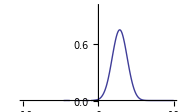

```mathematica
Plot[ψ[x],{x,-10,10},PlotRange->{0,1}]
```

```mathematica
|UCAT⟩=|-2,15⟩+|2,15⟩
```

1.9999 |0⟩+0. |1⟩+0.000141414 |2⟩+0. |3⟩+4.08228×10^-9 |4⟩+0. |5⟩+7.45319×10^-14 |6⟩+0. |7⟩+9.95974×10^-19 |8⟩+0. |9⟩+1.04985×10^-23 |10⟩+0. |11⟩+9.13776×10^-29 |12⟩+0. |13⟩+6.77336×10^-34 |14⟩+0. |15⟩

```mathematica
ψ[x_]=_x⟨x|·(|2.0,15⟩+|-2.0,15⟩)//Expand
```

0.0264623 ⅇ^(-x^2/2)+0. ⅇ^(-x^2/2) x+0.126502 ⅇ^(-x^2/2) x^2+0. ⅇ^(-x^2/2) x^3+0.0361436 ⅇ^(-x^2/2) x^4+0. ⅇ^(-x^2/2) x^5+0.0481914 ⅇ^(-x^2/2) x^6+0. ⅇ^(-x^2/2) x^7-0.00688449 ⅇ^(-x^2/2) x^8+0. ⅇ^(-x^2/2) x^9+0.00183586 ⅇ^(-x^2/2) x^10+0. ⅇ^(-x^2/2) x^11-0.000111264 ⅇ^(-x^2/2) x^12+0. ⅇ^(-x^2/2) x^13+4.89075×10^-6 ⅇ^(-x^2/2) x^14+0. ⅇ^(-x^2/2) x^15

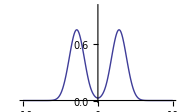

```mathematica
Plot[ψ[x],{x,-10,10},PlotRange->{0,1}]
```

### HO in a perturbing potential

```mathematica
Subscript[Ĥ, 0]=(P̂)^2/(2m)+1/2 m ω^2(X̂)^2;
```

```mathematica
X̂=1/(√2)(SuperDagger[â]+â);
```

```mathematica
Ŵ=σ ℏ  ω (X̂)^3//QAPowerExpand//Expand;
```

```mathematica
Operator/:SuperDagger[â]·|n_⟩:=√(n+1)|n+1⟩
Operator/:â·|n_⟩:=√n|n-1⟩
```

```mathematica
⟨n_|m_⟩:=KD[n,m]
```

```mathematica
KD[n_+b_.,n_+a_.]:=0/;a≠b
```

```mathematica
sum[A_+B_,{n_}]:=sum[A,{n}]+sum[B,{n}]
sum[x_. KD[n_,m_]^(k_.),{n_}]:= x /.n->m
sum[x_. KD[n_,m_]^(k_.),{m_}]:=x /.m->n
```

```mathematica
sum[f[n,m] KD[m,n+2]^3,{m}]
```

```mathematica
Subscript[ℰ, 0]=(n+1/2)ℏ ω
```

```mathematica
Subscript[ℰ, 1]=⟨n|·Ŵ·|n⟩//Expand
```

```mathematica
Subscript[ℰ, 2]=sum[(⟨m|·Ŵ·|n⟩)^2/((n-m)ℏ ω)//Expand,{m}]
```